```mathematica
CellularAutomaton[30,{0,0,0,1,0,0,0},4]
```

{{0,0,0,1,0,0,0},{0,0,1,1,1,0,0},{0,1,1,0,0,1,0},{1,1,0,1,1,1,1},{0,0,0,1,0,0,0}}

```mathematica
ArrayPlot[CellularAutomaton[30,RandomInteger[1,250],100]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},100]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[250,{{1},0},100]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[90,{{1},0},100]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[110,{{1},0},100]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[{867,{3,1},1},{{1},0},100]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[{Mod[Apply[Plus,#],4]&,{},1},{{1},0},100]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[{Mod[Total[#]+#2,4]&,{},1},{{1},0},100]]
```

-Graphics-

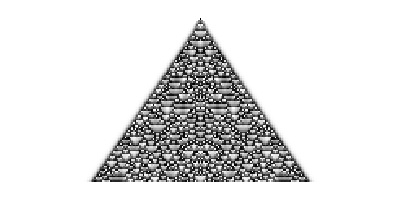

```mathematica
ArrayPlot[CellularAutomaton[{Mod[1/2 Apply[Plus,#],1]&,{},1},{{1},0},100]]
```

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},{{0,100,2}}]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[30,{{1},0},{100,{-20,100}}]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[225,{{1},0},100]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[225,{{1},0},{100,All}]]
```

-Graphics-

```mathematica
code797={797,{2,1},{1,1}};
ArrayPlot[First[CellularAutomaton[code797,{{{1}},0},{{70}}]]]
```

-Graphics-

```mathematica
ArrayPlot[Map[First,CellularAutomaton[code797,{{{1}},0},{70,{0},All}]]]
```

-Graphics-

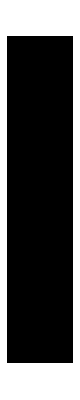
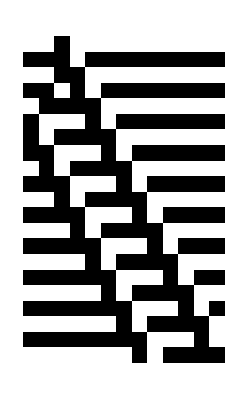
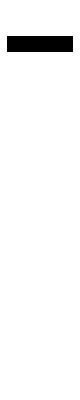
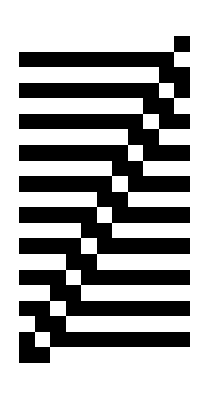
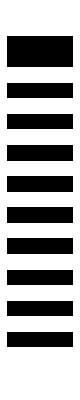
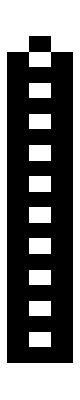
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[CellularAutomaton[#,{{1},0},20]]&/@Range[100,139]
```

```mathematica
ArrayPlot[CellularAutomaton[110,{{1},0},100]]
```

-Graphics-

```mathematica
Rotate[ArrayPlot[CellularAutomaton[135,{{1},0},40],Mesh->True],-45 Degree]
```

-Graphics-

```mathematica
Graphics[Rotate[First[ArrayPlot[CellularAutomaton[135,{{1},0},80],Mesh->True]],-45 Degree],PlotRange->{{83,104},{-12,60}}]
```

-Graphics-